```mathematica
(*
for putting into gamma_jet_reconnection.nb
qe->q
r0->radiuse
hpl->h
alphaf->alpha
*)
```

```mathematica
qe=4.8032*10^(-10)
me=9.1094*10^(-28)
c=2.9979*10^(10)
r0=2.8179402894*10^(-13)
kb=1.3807*10^(-16)
ergPmev=1.60217649*10^(-6)
hpl=4.13566733*10^(-15)*10^(-6)*ergPmev
hbar=hpl/(2*Pi);
alphaf=qe^2/(hbar*c)
sigmat=(8*Pi/3)*(qe^4/(me^2*c^4))
```

4.8032×10^-10

9.1094×10^-28

2.9979×10^10

2.81794×10^-13

1.3807×10^-16

1.60218×10^-6

6.62607×10^-27

0.0072974

6.65263×10^-25

```mathematica
CE[mug_,T_]:=Exp[-mug/(kb*T)]
Phi[eg_]:=me*c^2/eg
sigmagg[eg_,mug_]:=Module[{myphi,result},
myphi=Pi*r0^2*Phi[eg]^2*((2+2*Phi[eg]^2-Phi[eg]^4)*ArcCosh[1/Phi[eg]]-(1+Phi[eg]^2)*(1-Phi[eg]^2)^(1/2));
result=If[Phi[eg]<1,myphi,0];
(* return *)
result
];
(*xi[eg_]:=eg/(kb*T)*)
Theta[T_]:=kb*T/(me*c^2);
xi[eg_,T_]:=1/(Theta[T]*Phi[eg])
sigmaxi[xi_,mug_,T_]:=sigmagg[xi*kb*T,mug]
Clear[x];
halfsigmavgg[mug_?NumericQ,nmax_?NumericQ,lmax_?NumericQ,T_?NumericQ]:=Re[c*Sum[(1/(Sqrt[n*l]*CE[mug,T]^(n+1)))*NIntegrate[sigmaxi[x,mug,T]*x^4*BesselK[1,2*Sqrt[n*l]*x],{x,0,Infinity},AccuracyGoal->Infinity,PrecisionGoal->4],{n,1,nmax},{l,1,lmax}]]
(* Then Rgg = ng0^2*sigmavgg/2 *)
```

```mathematica
Tetype=me*c^2/kb
```

5.92959×10^9

0.5

1.32689×10^-25

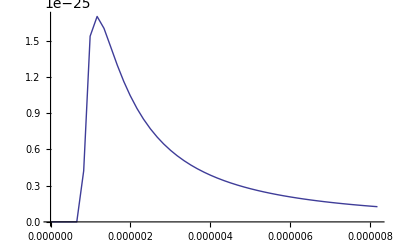

```mathematica
Phi[2*me*c^2]
sigmagg[2*me*c^2,0]
Plot[sigmagg[x,0],{x,0,10*me*c^2}]
```

```mathematica
myT=10^9;
Ekev=kb*myT/ergPmev*10^3
Ekev=1000
myT=Ekev/10^3*ergPmev/kb
halfsigmavgg[0,2,2,myT]
halfsigmavgg[0,3,3,myT]
halfsigmavgg[0,2,2,3*10^8]
halfsigmavgg[0,3,3,3*10^8]
```

86.1765

1000

1.16041×10^10

1.28065×10^-15

1.40512×10^-15

1.81962×10^-28

1.81962×10^-28

NIntegrate::inumr: The integrand x^4 BesselK[1, 2 √2 x] If[3.21896049843815`*^8/x < 1, myphi$19645206, 0] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 3.21896049843815`*^8}}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.5014312393878047`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::inumr: The integrand x^4 BesselK[1, 2 √2 x] If[3.21896049843815`*^8/x < 1, myphi$19645295, 0] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 3.21896049843815`*^8}}.

NIntegrate::inumr: The integrand x^4 BesselK[1, 4 x] If[3.21896049843815`*^8/x < 1, myphi$19645347, 0] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 3.21896049843815`*^8}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.5014312393878047`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

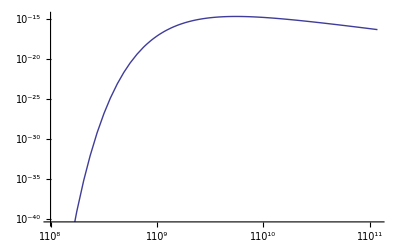

```mathematica
p1=LogLogPlot[halfsigmavgg[0,2,2,x],{x,10^8,20*me*c^2/kb}]
```

```mathematica
(* omega = Eg/(me*c^2) *)
sigmage2pair[omega_?NumericQ]:=Module[{parta,partb,partc,partd,prefactor,result},
prefactor=(sigmat*3*alphaf/(8*Pi));
parta[w_]:=(5.6+20.4*(omega-4)-10.9*(omega-4)^2-3.6*(omega-4)^3+7.4*(omega-4)^4)*10^(-3)*(omega-4)^2;
partb[w_]:=0.582814-0.29842*omega+0.04354*omega^2-0.0012977*omega^3;
partc[w_]:=(3.1247-1.3397*omega+0.14612*omega^2)/(1+0.4648*omega+0.016683*omega^2);
partd[w_]:=(84*Log[2*omega]-218)/27+(-1.333*Log[2*omega]^3+3.863*Log[2*omega]^2-11*Log[2*omega]+27.9)/omega;
result=If[omega<=4,0,If[omega>4&&omega<=4.6,parta[omega],If[omega>4.6&&omega≤6.0,partb[omega],If[omega>6.0&&omega≤14,partc[omega],partd[omega]]]]];
result=result*prefactor;
(* return *)
result
];
(* test *)
(*Plot[sigmage2pair[x],{x,0,20}]*)

ngam[mug_,nmax_,T_]:=16*Pi*(kb*T)^3/(hpl*c)^3*Sum[1/(n^3*CE[mug,T]^n),{n,1,nmax}];
fg[pg_,mug_,nmax_,T_]:=8*Pi*me*c^2/((hpl*c)^3*ngam[mug,nmax,T])*(pg*c)^2/(CE[mug,T]*Exp[pg*c/(kb*T)]-1);
(* p for electron *)
pge[eg_]:=(eg^2-me^2*c^4)/c^2;
(* p for photon *)
pgg[eg_]:=eg/c;
(* fgenx is x that is Eg/(me*c^2) *)
fgx[x_?NumericQ,mug_?NumericQ,nmax_?NumericQ,T_?NumericQ]:=fg[pgg[x*me*c^2],mug,nmax,T];
(* below should be 1 if did right thing *)
isone[T_]:=NIntegrate[fgx[x,0,3,T],{x,0,Infinity}];
(* x = Eg/(me*c^2) *)
(* ,AccuracyGoal->Infinity,PrecisionGoal->4]*)
(*
sigmaveg[mug_,nmax_,T_]:=(sigmat*c)/(2*BesselK[2,1/Theta[T]])*NIntegrate[fgx[x,mug,nmax,T]/x^2*NIntegrate[xr*sigmage2pair[xr]/sigmat*Exp[-(x/xr+xr/x)/(2*Theta[T])],{xr,4,Infinity},AccuracyGoal->Infinity,PrecisionGoal->4],{x,0,Infinity},AccuracyGoal->Infinity,PrecisionGoal->4]
*)
sigmaveg[mug_,nmax_,T_]:=(sigmat*c)/(2*BesselK[2,1/Theta[T]])*NIntegrate[fgx[x,mug,nmax,T]/x^2*xr*sigmage2pair[xr]/sigmat*Exp[-(x/xr+xr/x)/(2*Theta[T])],{xr,4,Infinity},{x,0,Infinity},AccuracyGoal->Infinity,PrecisionGoal->4]
(* then Rge=sigmaveg*ne*ng0 *)
```

```mathematica
myT=me*c^2/kb
myeg=myT*kb
mypg=myeg/c
isone[myT]
ngam[0,3,myT]
fg[mypg,0,3,myT]
fgx[1,0,3,myT]
```

5.92959×10^9

8.18699×10^-7

2.73091×10^-17

1.03444

4.08924×10^30

0.250412

0.250412

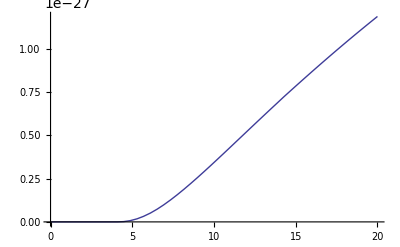

```mathematica
Plot[sigmage2pair[x],{x,0,20}]
```

```mathematica
sigmaveg[0,1,myT]
sigmaveg[0,2,myT]
sigmaveg[0,3,myT]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.9193×10^-17

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.70605×10^-17

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.65167×10^-17

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in xr near {xr, x} = {4.499998476876463`, 0.18466063387559606`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

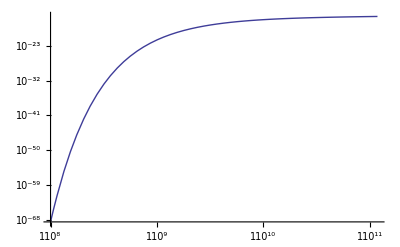

```mathematica
p2=LogLogPlot[sigmaveg[0,2,x],{x,10^8,20*me*c^2/kb}]
```

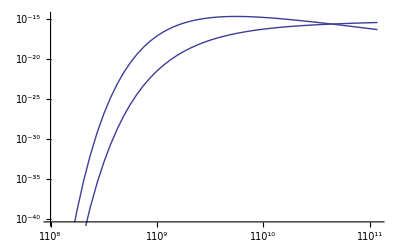

```mathematica
Show[{p1,p2}]
```

```mathematica
sigmavee2pairs[T_]:=Module[{foo,result,myresult},
result[Tx_]:=8.4*10^(-6)*sigmat*c*(Log[Theta[Tx]])^3;
myresult=If[Theta[T]≥1,result[T],0];
(* return *)
myresult
];
```

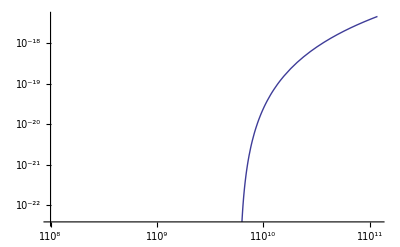

```mathematica
p3=LogLogPlot[sigmavee2pairs[x],{x,10^8,20*me*c^2/kb}]
```

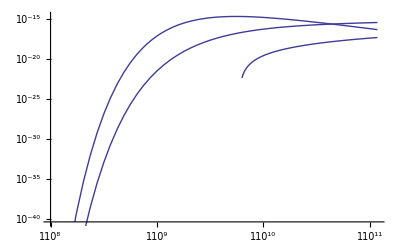

```mathematica
Show[{p1,p2,p3}]
```